```mathematica
r[u_,v_]:={Cos[v]-u*Sin[v],u*Cos[v]+Sin[v],u+v}
ru[u_,v_]:=D[r[u,v],u]
rv[u_,v_]:=D[r[u,v],v]
```

```mathematica
ruu[u_,v_]:=D[ru[u,v],u]
rvv[u_,v_]:=D[rv[u,v],v]
ruv[u_,v_]:=D[ru[u,v],v]//Simplify
n[u_,v_]:=ru[u,v]×rv[u,v]
```

```mathematica
ruv[u,v].n[u,v] //FullSimplify
```

-Cos[v] Sin[v] (Cos[v]+u Cos[v]+Sin[v]-u Sin[v])

```mathematica
(*SurfaceData[{r[u,v]},{"FirstFundamentalForm"}]
```

SurfaceData::notent: {{Cos[v]-u Sin[v],u Cos[v]+Sin[v],u+v}} is not a known entity, class, or tag for SurfaceData. Use SurfaceData[] for a list of entities.

SurfaceData[{{Cos[v]-u Sin[v],u Cos[v]+Sin[v],u+v}},{FirstFundamentalForm}]

```mathematica
f[x_,y_]:=a11*x^2+2a12*xy +a22*y^2+a1*x + a2*y+a0 
ContourPlot[{f[x,y]==0,f[1,1]==0,f[2,2]==0,f[3,3]==0,f[4,4]==0,f[5,5]==0},{x,-10,10},{y,-10,10}]
```

-Graphics-

{{c→0,a→-1}}

0

-1

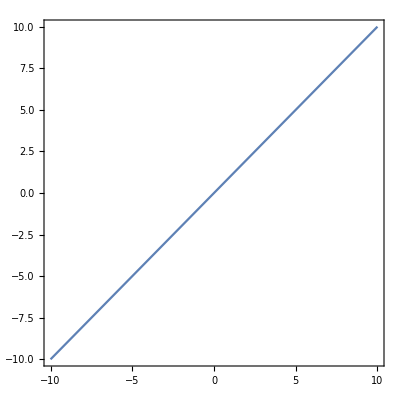

```mathematica
sol = Solve[{c==0 && a+c+1==0},{c,a}]
c = sol⟦1⟧⟦1⟧⟦2⟧
a = sol⟦1⟧⟦2⟧⟦2⟧
g[x_,y_]:=a*x+y+c
ContourPlot[{{g[x,y]==0}},{x,-10,10},{y,-10,10}]
```

```mathematica
Solve[{x,y}∈InfiniteLine[{{0,0},{2,1}}]&&{x,y}∈Circle[],{x,y}];
Graphics[{{Blue,InfiniteLine[{{0,0},{2,1}}],Circle[]},{PointSize[Large],Red,Point[{x,y}]/.%}}]
```

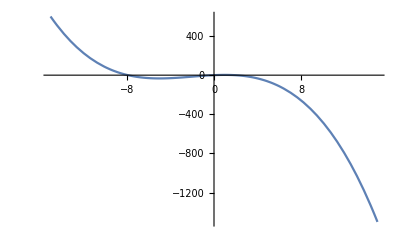

```mathematica
g[x_]:=-x^3/3 -2 x^2+5x;
Plot[g[x],{x,-15,15}]
```

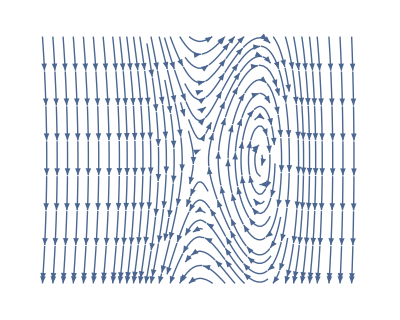

```mathematica
StreamPlot[{y,g[x]},{x,-5,5},{y,-3,3},Frame->None,StreamPoints->Fine,AspectRatio->0.8]
```